0.706396

0.785316

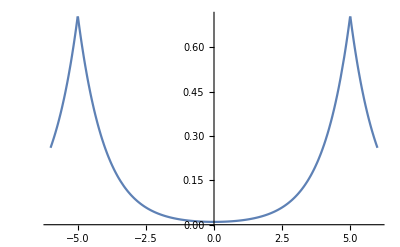

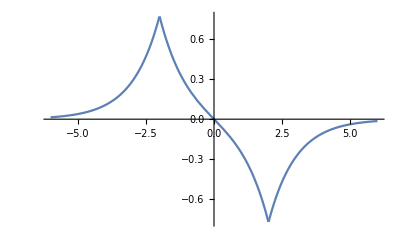

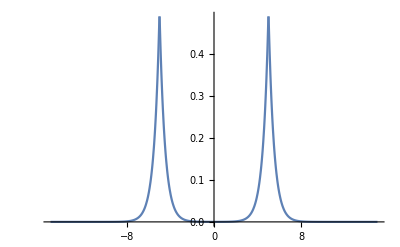

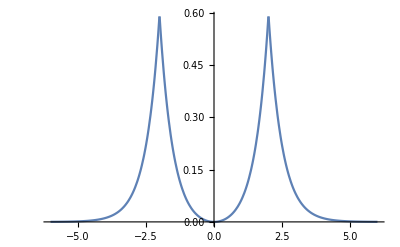

```mathematica
puskar[x_,y_,z_]:=Pi^(-1/2)*(Exp[-Sqrt[x^2+y^2+(z+5)^2]]+Exp[-Sqrt[x^2+y^2+(z-5)^2]]);
bhattarai[x_,y_,z_]:=Pi^(-1/2)*(Exp[-Sqrt[x^2+y^2+(z+2)^2]]-Exp[-Sqrt[x^2+y^2+(z-2)^2]]);
normP=NIntegrate[(puskar[x,y,z])^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}];
normM=NIntegrate[(bhattarai[x,y,z])^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}];
normP=1.0/Sqrt[normP]
normM=1.0/Sqrt[normM]
puskar[x_,y_,z_]:=normP*(Exp[-Sqrt[x^2+y^2+(z+5)^2]]+Exp[-Sqrt[x^2+y^2+(z-5)^2]])
bhattarai[x_,y_,z_]:=normM*(Exp[-Sqrt[x^2+y^2+(z+2)^2]]-Exp[-Sqrt[x^2+y^2+(z-2)^2]])
Plot[puskar[0,0,z],{z,-6,6},PlotRange->All]
Plot[bhattarai[0,0,z],{z,-6,6},PlotRange->All]
Plot[(puskar[0,0,z])^2,{z,-15,15},PlotRange->All]
Plot[(bhattarai[0,0,z])^2,{z,-6,6},PlotRange->All]
```

```mathematica
del[R_]:=(1+R+R^2/3)*Exp[-R]
Nplus[R_]:=(2*(1-del[R]))^(-1/2)
Evaluate[Nplus[4]]
```

1/(√(2 (1-31/(3 ⅇ^4))))

```mathematica
N[1/(√(2 (1-31/(3 ⅇ^4))))]
```

0.785316

```mathematica
N[1/(√(2 (1+31/(3 ⅇ^4))))]
```

0.648405

```mathematica
NIntegrate[(puskar[0,0,z])^2,{z,0,Infinity}]
```

1.40601

```mathematica
NIntegrate[(bhattarai[0,0,z])^2,{z,0,Infinity}]
```

0.71817

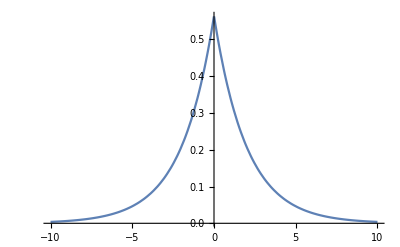

```mathematica
Plot[1/Sqrt[Pi]*Exp[-1/2*Sqrt[z^2]],{z,-10,10},PlotRange->All]
```